```mathematica
Clear[m1,m2,m,L,V,k,En,r];
μ=(m1*m2)/(m1+m2);En=(μ*V^2)/2;Lrel=2*μ*L*V;
m1=m2=m=L=1;
V=0.1;
k=1;
U=-k*(m1 m2)/r[t];
```

```mathematica
solr=NDSolve[{μ*r''[t]==Lrel^2/(μ*r[t]^3)-D[U, r[t]],r[0]==1,r'[0]==0}, r, {t,0,100}][[1,1,2]];
solq=NDSolve[{theta'[t]==(2L*V)/solr[t]^2,theta[0]==0},theta,{t,0,100}][[1,1,2]];
```

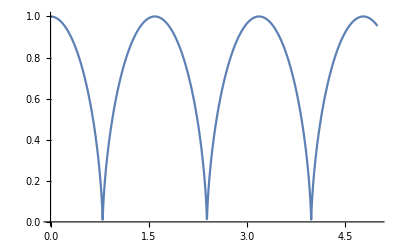

```mathematica
Plot[solr[x],{x,0.,5.}]
```

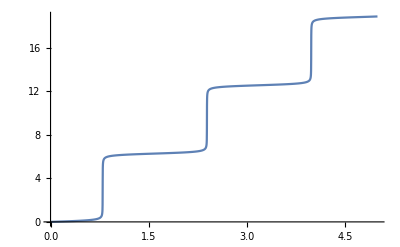

```mathematica
Plot[solq[x],{x,0.,5.}]
```

```mathematica
x[t_]:=Cos[solq[t]]*solr[t];
y[t_]:=Sin[solq[t]]*solr[t];
x1p[t_]:=m2/(m1+m2)x[t];
y1p[t_]:=m2/(m1+m2)y[t];
x2p[t_]:=-m1/(m1+m2)x[t];
y2p[t_]:=-m1/(m1+m2)y[t];
```

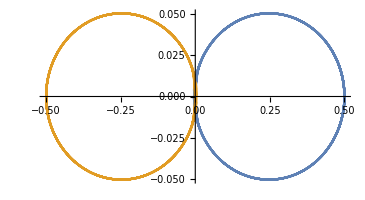

```mathematica
ParametricPlot[{{x1p[t],y1p[t]},{x2p[t],y2p[t]}},{t,0,10}]
```

```mathematica
Animate[ParametricPlot[{{x1p[t],y1p[t]},{x2p[t],y2p[t]}},{t,0,a}, Epilog->{{PointSize[Large],Blue, Point[{x1p[a],y1p[a]}]},{PointSize[Large],Orange, Point[{x2p[a],y2p[a]}]}},PlotRange->{{-0.6,0.6},{-0.6,0.6}},Axes->False],{a,0,100},AnimationRate->0.6]
```